## Definiciones

```mathematica
Needs["QMB`"]
```

```mathematica
DimH[xc_]:=2*Sum[VerticalBoundary[x,xc]+1,{x,0,2*xc}]
```

```mathematica
TagPosition[ket_,tags_]:=FirstPosition[tags,Tag[ket]]
```

```mathematica
ClearAll[HorizontalBoundary,VerticalBoundary]

HorizontalBoundary[y_,xc_]:=Round[xc+Sqrt[xc^2-y^2]]
HorizontalBoundary[y_,xc_,yu_]:=Round[xc+Sqrt[yu^2-y^2]]

VerticalBoundary[x_,xc_]:=If[x<=xc,xc,Round[Sqrt[xc^2-(x-xc)^2]]]
VerticalBoundary[x_,xc_,yu_]:=If[x<=xc,yu,Round[Sqrt[yu^2-(x-xc)^2]]]
```

```mathematica
Basis[xc_]:=Flatten[Table[{x,y,c},{x,0,2*xc},{y,0,VerticalBoundary[x,xc]},{c,0,1}],2]
```

```mathematica
(* xc: length of square part of the stadium, tags: tags of position basis kets *)
VerticalShift[xc_,tags_]:=
Module[{ymax},
SparseArray[Transpose[{Flatten[
Table[
ymax=VerticalBoundary[x,xc];
Join[
(* y = 0 *)
{If[ymax==0.,TagPosition[{x,0.,1.},tags],TagPosition[{x,1.,0.},tags]],TagPosition[{x,0.,0.},tags]},
(* 1 <= y < ymax *)
Table[
{TagPosition[{x,y+1.,0.},tags],TagPosition[{x,y-1.,1.},tags]}
,{y,1.,ymax-1}],
(* y = ymax *)
If[ymax>0.,TagPosition[#,tags]&/@{{x,ymax,1.},{x,ymax-1.,1.}},{}]
]
,{x,0.,2.*xc}]
],Range[DimH[xc]]}]->1.]
]
```

```mathematica
ClearAll[HorizontalShift]
HorizontalShift[xc_,tags_,reversedBasis_]:=
Module[{ymax,xmax},
SparseArray[Transpose[{Flatten[
Table[
ymax=VerticalBoundary[x,xc];
Table[
xmax=HorizontalBoundary2[y,reversedBasis];
Which[x==0.,{TagPosition[{1.,y,0.},tags],TagPosition[{0.,y,0.},tags]},x==xmax,{TagPosition[{x,y,1.},tags],TagPosition[{x-1.,y,1.},tags]},1<=x<xmax,{TagPosition[{x+1.,y,0.},tags],TagPosition[{x-1.,y,1.},tags]}]
,{y,0.,ymax}]
,{x,0.,2.*xc}]
],Range[DimH[xc]]}]->1.]
]
```

```mathematica
HorizontalBoundary2[y_,reversedBasis_]:=SelectFirst[reversedBasis,#[[2]]==y&][[1]]
```

```mathematica
Coin[α_,xc_]:=KroneckerProduct[IdentityMatrix[Round[DimH[xc]]/2,SparseArray],SparseArray[{{Cos[α],Sin[α]},{-Sin[α],Cos[α]}}]]
```

```mathematica
Coin2[α_,xc_]:=KroneckerProduct[IdentityMatrix[Round[DimH[xc]]/2,SparseArray],SparseArray[{{Cos[α],Sin[α]},{-Sin[α],Cos[α]}}]]
```

```mathematica
α=Pi/4.;cc=KroneckerProduct[IdentityMatrix[Round[DimH[xc]]/2,SparseArray],SparseArray[{{Cos[α],Sin[α]},{-Sin[α],Cos[α]}}]]
```

KroneckerProduct[IdentityMatrix[1/2 Round[2 ∑_(x=0)^(2 xc) (1+If[x≤xc,xc,Round[√(xc^2-(x-xc)^2)]])],SparseArray],SparseArray[…]]

```mathematica
cc//MatrixForm
```

KroneckerProduct[IdentityMatrix[1/2 Round[2 ∑_(x=0)^(2 xc) (1+If[x≤xc,xc,Round[√(xc^2-(x-xc)^2)]])],SparseArray],SparseArray[…]]

## Vertical shift (en el paper x_c=m_c, considero 2 x_c=m_r y y_u=n_u=x_c como en el paper)

Ejemplo para x_c=1 (en el paper x_c=m_c)

```mathematica
xc=1;

(* Elementos de la base de posición *)
basis=Basis[xc]

(* Tags de la base *)
tags=Tag/@basis

(HV=VerticalShift[xc,tags])//MatrixForm
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1},{2,0,0},{2,0,1}}

{0.,14.2478,10.1489,24.3967,1.73205,15.9799,11.8809,26.1287,3.4641,17.7119}

(0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0)

Escalamiento del tiempo de cómputo:

```mathematica
Table[basis=Basis[xc];tags=Tag/@basis;AbsoluteTiming[{xc,VerticalShift[xc,tags]}],{xc,25,50,5}]
```

{{0.002902,{5,SparseArray[…]}},{0.014788,{10,SparseArray[…]}},{0.043296,{15,SparseArray[…]}},{0.11089,{20,SparseArray[…]}},{0.23153,{25,SparseArray[…]}}}

Memoria máxima que usa para x_c=75 (misma del paper, en el paper x_c=m_c)

```mathematica
xc=75;MaxMemoryUsed[basis=Basis[xc];tags=Tag/@basis;AbsoluteTiming[{xc,VerticalShift[xc,tags]}]]/10.^9
```

0.00593889

Tiempo de cómputo:

```mathematica
basis=Basis[xc];tags=Tag/@basis;AbsoluteTiming[{xc,VerticalShift[xc,tags]}]
```

{14.2392,{75,SparseArray[…]}}

## Horizonatal shift

```mathematica
basis=Basis[1.]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1},{2,0,0},{2,0,1}}

```mathematica
Tag/@basis//DeleteDuplicates//Length
```

10

```mathematica
(*Horizontal shift matrix*)
HS=Module[{ymax,xc=1.,tags=Tag/@basis},
SparseArray[Transpose[{Flatten[
Table[
ymax=VerticalBoundary[x,xc];
(* 1 <= y < ymax *)
Table[
Which[x==0.,{TagPosition[{1.,y,0.},tags],TagPosition[{0.,y,0.},tags]},x==HorizontalBoundary[y,xc],{TagPosition[{x,y,1.},tags],TagPosition[{x-1.,y,1.},tags]},1<=x<HorizontalBoundary[y,xc],{TagPosition[{x+1.,y,0.},tags],TagPosition[{x-1.,y,1.},tags]}]
,{y,0.,ymax}]
,{x,0.,2.*xc}]
],Range[DimH[xc]]}]->1.]
]
```

SparseArray[…]

Hace lo que tiene que hacer:

```mathematica
Position[HS.#,1.]&/@IdentityMatrix[10]
```

{{{5}},{{1}},{{7}},{{3}},{{9}},{{2}},{{8}},{{4}},{{10}},{{6}}}

La nueva definición también:

```mathematica
xc=1.;
basis=Basis[xc];reversedBasis=Reverse[basis];
tags=Tag/@basis;
HS=HorizontalShift[xc,tags,reversedBasis]
Position[HS.#,1.]&/@IdentityMatrix[10]
```

SparseArray[…]

{{{5}},{{1}},{{7}},{{3}},{{9}},{{2}},{{8}},{{4}},{{10}},{{6}}}

```mathematica
xc=50.;
basis=Basis[xc];reversedBasis=Reverse[basis];
tags=Tag/@basis;
{RepeatedTiming[HorizontalShift[xc,tags,reversedBasis]],RepeatedTiming[VerticalShift[xc,tags]]}
```

{{26.3287,SparseArray[…]},{19.0549,SparseArray[…]}}

```mathematica
xc=50.;
basis=Basis[xc];reversedBasis=Reverse[basis];
tags=Tag/@basis;
c=Coin[Pi/8.,xc];

sh=HorizontalShift[xc,tags,reversedBasis];
sv=VerticalShift[xc,tags];

AbsoluteTiming[U=sh.c.sv.c]
```

{0.011811,SparseArray[…]}

```mathematica
ψ0=Flatten@KroneckerProduct[Join[{1.},ConstantArray[0.,9180/2-1]],{0.,1.}];
```

```mathematica
ψ0=SparseArray[2->1.,9180]
```

SparseArray[…]

```mathematica
MatrixPartialTrace[Dyad[U.U.U.U.U.ψ0],1,{9180/2,2}]//MatrixForm
```

(0.804575 | 0.0278534
0.0278534 | 0.195425)

```mathematica
Purity[MatrixPartialTrace[Dyad[#],1,{9180/2,2}]]&/@NestList[U.#&,ψ0,20]
```

{1.,1.,0.813285,0.675724,0.697503,0.687083,0.713366,0.718757,0.729066,0.738983,0.738489,0.734551,0.734824,0.734199,0.737817,0.73938,0.741681,0.744625,0.744735,0.743433,0.74344}

```mathematica
eigvals=Eigenvalues[U];
```

```mathematica
eigphases=Sort[Mod[Arg[#],2Pi]&/@eigvals];
```

```mathematica
s=(#-RotateRight[#]&[eigphases])[[2;;]];
```

```mathematica
Mean[s]
```

0.000684517

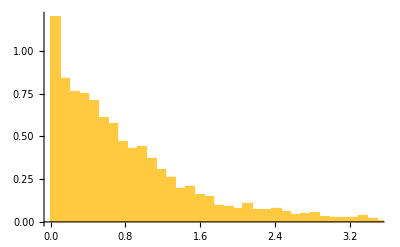

```mathematica
Histogram[s/Mean[s],Automatic,"PDF"]
```

## Aquí para exportar

```mathematica
Pi/4.-Pi/4.+0.05
```

0.05

```mathematica
Pi/4.
Pi/3.
```

0.785398

1.0472

```mathematica
xc=50.;
basis=Basis[xc];reversedBasis=Reverse[basis];
tags=Tag/@basis;
c1=Coin[Pi/5.,xc];
c2=Coin[-4Pi/5,xc];

sh=HorizontalShift[xc,tags,reversedBasis];
sv=VerticalShift[xc,tags];

AbsoluteTiming[U=Normal[sh.c2.sv.c1];]
```

{0.418162,Null}

```mathematica
eigvals=Eigenvalues[U];
```

```mathematica
ephases5=Sort[Mod[#,2Pi]&/@Arg[eigvals]];
```

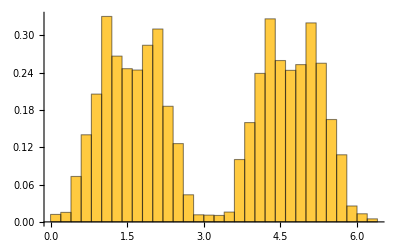

```mathematica
Histogram[ephases,Automatic,"PDF"]
```

```mathematica
Import["/home/jadeleon/Documents/libs/QMB.wl"]
```

```mathematica
ephasesCOE=Sort[Mod[#,2Pi]&/@Arg[Eigenvalues[RandomVariate[CircularOrthogonalMatrixDistribution[4000]]]]];
```

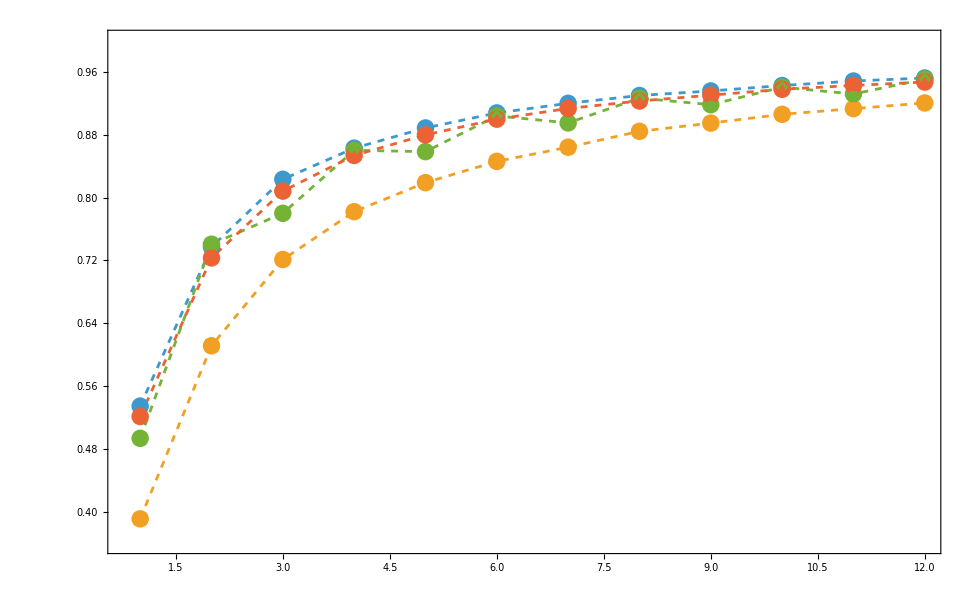

```mathematica
ratiosCOE=Table[{k,Mean[If[#=={0.,0.},Nothing,Min[#]/Max[#]]&/@Transpose[{RotateLeft[#],#}&[kthOrderSpacings[ephasesCOE,k]]]]},{k,12}];
ratiosPoisson=Table[{k,Mean[If[#=={0.,0.},Nothing,Min[#]/Max[#]]&/@Transpose[{RotateLeft[#],#}&[kthOrderSpacings[Sort[RandomReal[{-1,1},5000]],k]]]]},{k,12}];
ratios=Table[{k,Mean[If[#=={0.,0.},Nothing,Min[#]/Max[#]]&/@Transpose[{RotateLeft[#],#}&[kthOrderSpacings[ephases,k]]]]},{k,12}];
ratios2=Table[{k,Mean[If[#=={0.,0.},Nothing,Min[#]/Max[#]]&/@Transpose[{RotateLeft[#],#}&[kthOrderSpacings[ephases2,k]]]]},{k,12}];
ListPlot[{ratiosCOE,ratiosPoisson,ratios,ratios2},PlotRange->{All,{0.36,1.}},Joined->True,Mesh->True,PlotMarkers->{Automatic, 13},PlotStyle->Directive[Dashed],Frame->True]
```

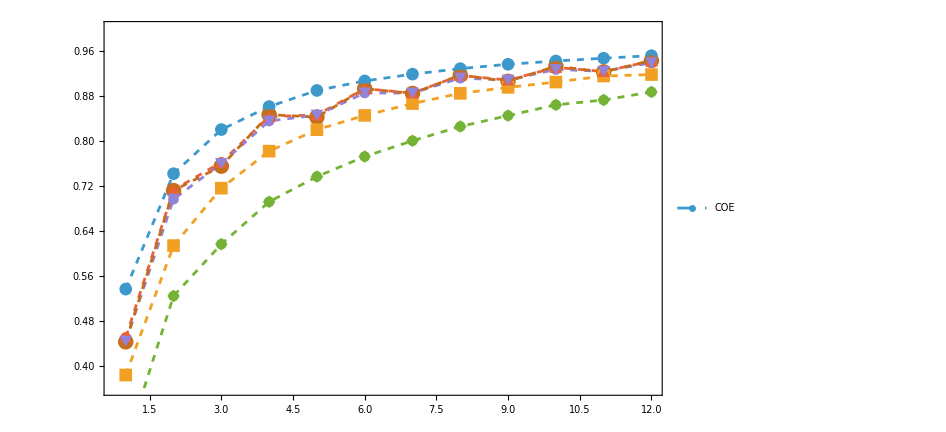

```mathematica
ratiosCOE=Table[{k,Mean[If[#=={0.,0.},Nothing,Min[#]/Max[#]]&/@Transpose[{RotateLeft[#],#}&[kthOrderSpacings[ephasesCOE,k]]]]},{k,12}];
ratiosPoisson=Table[{k,Mean[If[#=={0.,0.},Nothing,Min[#]/Max[#]]&/@Transpose[{RotateLeft[#],#}&[kthOrderSpacings[Sort[RandomReal[{-1,1},5000]],k]]]]},{k,12}];
ratios=Table[{k,Mean[If[#=={0.,0.},Nothing,Min[#]/Max[#]]&/@Transpose[{RotateLeft[#],#}&[kthOrderSpacings[ephases,k]]]]},{k,12}];
ratios2=Table[{k,Mean[If[#=={0.,0.},Nothing,Min[#]/Max[#]]&/@Transpose[{RotateLeft[#],#}&[kthOrderSpacings[ephases2,k]]]]},{k,12}];
ratios3=Table[{k,Mean[If[#=={0.,0.},Nothing,Min[#]/Max[#]]&/@Transpose[{RotateLeft[#],#}&[kthOrderSpacings[ephases3,k]]]]},{k,12}];
ratios4=Table[{k,Mean[If[#=={0.,0.},Nothing,Min[#]/Max[#]]&/@Transpose[{RotateLeft[#],#}&[kthOrderSpacings[ephases4,k]]]]},{k,12}];
ratios5=Table[{k,Mean[If[#=={0.,0.},Nothing,Min[#]/Max[#]]&/@Transpose[{RotateLeft[#],#}&[kthOrderSpacings[ephases5,k]]]]},{k,12}];
ListPlot[{ratiosCOE,ratiosPoisson,ratios,ratios2,ratios4,ratios5},PlotRange->{All,{0.36,1.}},Joined->True,Mesh->True,PlotMarkers->{Automatic, 13},PlotStyle->Directive[Dashed],Frame->True,FrameStyle->Directive[Black,FontSize->28],FrameLabel->{"", ""},PlotLegends->Placed[LineLegend[{"COE","","","",""},LabelStyle->FontSize->23], {Right,Bottom}],ImageSize->700]
```

### Tratando de replicar datos de antes

```mathematica
xc=50.;
basis=Basis[xc];reversedBasis=Reverse[basis];
tags=Tag/@basis;
c1=Coin[Pi/4.,xc];
c2=Coin[Pi/6.,xc];

sh=HorizontalShift[xc,tags,reversedBasis];
sv=VerticalShift[xc,tags];

AbsoluteTiming[U=Normal[sh.c2.sv.c1];]
```

{0.299521,Null}

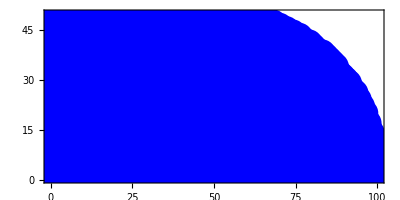

```mathematica
ListPlot[DeleteDuplicates[basis[[All,{1,2}]]],PlotStyle->{PointSize[0.05],Blue},AspectRatio->Automatic,Frame->True]
```

```mathematica
eigvals=Eigenvalues[U];
```

```mathematica
Export["/home/jadeleon/Documents/chaotic_walks/eigvals_U_xc_50_alpha_Pi-4_beta_Pi-6.csv",eigvals,"CSV"]
```

/home/jadeleon/Documents/chaotic_walks/eigvals_U_xc_50_alpha_Pi-4_beta_Pi-6.csv

```mathematica
eigphases=Sort[Mod[Arg[#],2Pi]&/@eigvals];
```

```mathematica
r=Ratios[Differences[eigphases[[1000;;-1000]]]];
```

```mathematica
rr=Min/@Transpose[{r,1/r}];
```

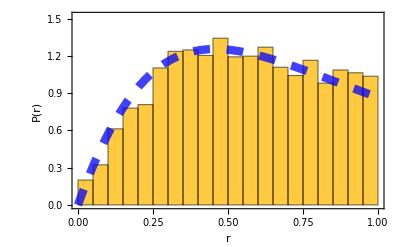

```mathematica
Show[Histogram[rr,Automatic,"PDF",PlotRange->{{0,1.},{0,1.52}},Frame->True,FrameStyle->Directive[Black,FontSize->20],FrameLabel->{"r", "P(r)"}],Plot[27/4*(r+r^2)/((1+r+r^2)^(5/2)),{r,0,1},PlotStyle->Directive[Blue,Thickness[0.015],Dashing[0.03],Opacity[0.75]]],(*The legends in the Epilog are starting here*)Epilog->Inset[Framed[Column[{LineLegend[{Directive[Blue,Thickness[0.015],Dashing[0.03]]},{"GOE"}]}],RoundingRadius->3],Scaled[{0.82,0.85}]]
(*End of the Legends*)]
```

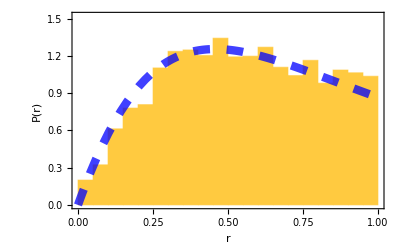

```mathematica
Show[Histogram[rr,Automatic,"PDF",PlotRange->{{0,1.},{0,1.52}},Frame->True,FrameStyle->Directive[Black,FontSize->20],FrameLabel->{"r", "P(r)"}],Plot[27/4*(r+r^2)/((1+r+r^2)^(5/2)),{r,0,1},PlotStyle->Directive[Blue,Thickness[0.015],Dashing[0.03],Opacity[0.75]]],(*The legends in the Epilog are starting here*)Epilog->Inset[Framed[Column[{LineLegend[{Directive[Blue,Thickness[0.015],Dashing[0.03]]},{"GOE"}]}],RoundingRadius->3],Scaled[{0.82,0.85}]]
(*End of the Legends*)]
```

```mathematica
MeanLevelSpacingRatio[eigphases[[#*100;;#*-100]]]&/@Range[10]
```

{0.488813,0.49893,0.508115,0.516948,0.525382,0.533373,0.539749,0.54451,0.548559,0.551269}

```mathematica
MeanLevelSpacingRatio[eigphases[[650;;-650]]]
```

0.536507

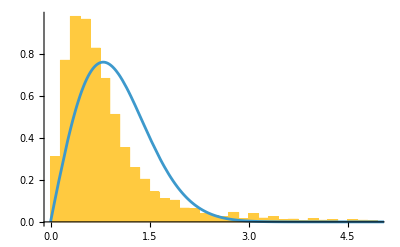

```mathematica
eigphases=Sort[Mod[Arg[#],2Pi]&/@eigvals];
s=Differences[eigphases[[2000;;-2000]]];
s=s/(Mean[s]);
Show[Histogram[s,{0,5,0.15},"PDF"],Plot[Pi/2s Exp[-Pi s^2/4],{s,0,2Pi}]]
```

```mathematica
eigphases[[2000;;-2000]][[1;;10]]
```

{1.45941,1.45983,1.46036,1.46069,1.46078,1.46153,1.46214,1.46216,1.46247,1.46313}

```mathematica
0.1*Length[s]
```

917.9

```mathematica
MinMax[Chop[s]]
```

{0,15.4597}

```mathematica
eigphases[[1;;2]]
```

{0.00256454,0.00769291}

```mathematica
Differences[eigphases[[1;;2]]]
```

{0.00512837}

```mathematica
BinCounts[s,{0,3,0.1}]
```

{284,822,974,1066,894,780,682,548,418,350,264,192,190,152,144,122,110,76,70,72,66,46,38,48,38,32,48,24,42,34}

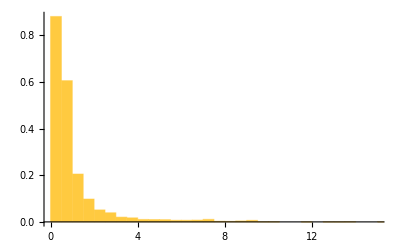

```mathematica
Histogram[s,{0,100,0.5},"PDF",PlotRange->{{0,15},All}]
```

```mathematica
MinMax[s]
```

{2.59717×10^-12,15.4597}

```mathematica
3.5*StandardDeviation[s]/CubeRoot[Length[s]]
```

0.235274

9179^(1/3)

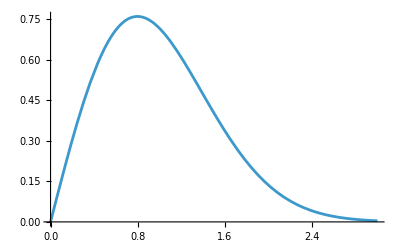

```mathematica
Plot[Pi/2s Exp[-Pi s^2/4],{s,0,3}]
```